```mathematica
Quit[]
```

# Calculations

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.0 (development version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

Calculations

## Initial constants

```mathematica
Y=1/2;
Gf=1.166*10^(-5);
dm232=1;
a1=1.07;
Fm2320=1/(3*π);
mπ=0.13957;
fπ=0.1304;
mρ=0.7665;
fρ=0.216;
ma1=1.230;
fa1=0.238;
SetAttributes[V,Orderless];
V["c","b"]=0.0411;V["c","s"]=0.974;V["c","d"]=0.225;
V["u","b"]=0.00357;V["u","s"]=0.225;V["u","d"]=0.974;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Fq2π=ReadList["plot2pi.txt",{Number,Number}];
Fq3π=ReadList["plot3pi.txt",{Number,Number}];
Fq4π=ReadList["plot4pi.txt",{Number,Number}];
Fq5π=ReadList["plot5pi.txt",{Number,Number}];
Fq4πinterference=ReadList["interf.txt",{Number,Number}];
```

## Initial Tau lepton calculations for constants

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p1,p2]=(m1^2+m2^2-q2)/2;
q=p1-p2;
H =SpinorUBar[p2,m2].GA[μ].(1+GA[5]).SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
H2=H*cH;
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[q,μ]*FV[q,α]-q2*MT[μ,α])]];
λ:=√(1-((m2+√q2)/m1)^2)*√(1-((m2-√q2)/m1)^2);
HT:=λ*H4;
m1=1.776;
m2=0;
h=6.5*10^-25;τ=290*10^-15;
Γτ=h/τ;
```

```mathematica
(*Decay to 2π*)
Clear[Br, BrNorm];
BrNorm=0.2549;
dΓ2π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq2π][q2];
Γ2π=NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Const2π=BrNorm/Br
Γ2π=Const2π*NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Error=Br/BrNorm
```

0.35257

1.

```mathematica
Clear[Br];
BWr[qsum_]:=Module[{ret,mRho,gammaRho,mRhopr,gammaRhopr,beta,m1,m2,mQ2,dRho,pPiRho,dRhopr,pPiRhopr,dQ,pPiQ,BRhoDem,BRho,BRhoprDem,BRhopr},mRho=0.775;
gammaRho=0.149;
mRhopr=1.364;
gammaRhopr=0.400;
beta=-0.108;
m1=0.13957018;m2=0.13957018;
mQ2=qsum*qsum;(*?*)dRho=mRho*mRho-m1*m1-m2*m2;
pPiRho=(1.0/mRho)*Sqrt[(dRho*dRho)/4.0-m1*m1*m2*m2];
dRhopr=mRhopr*mRhopr-m1*m1-m2*m2;
pPiRhopr=(1.0/mRhopr)*Sqrt[(dRhopr*dRhopr)/4.0-m1*m1*m2*m2];
dQ=mQ2-m1*m1-m2*m2;
pPiQ=(1.0/Sqrt[mQ2])*Sqrt[(dQ*dQ)/4.0-m1*m1*m2*m2];
gammaRho=gammaRho*mRho/Sqrt[mQ2]*Power[(pPiQ/pPiRho),3];
BRhoDem=mRho*mRho-mQ2+I*(-1.0*mRho*gammaRho);
BRho=mRho*mRho/BRhoDem;
gammaRhopr=gammaRhopr*mRhopr/Sqrt[mQ2]*Power[(pPiQ/pPiRhopr),3];
BRhoprDem=mRhopr*mRhopr-mQ2+I*(-1.0*mRho*gammaRhopr);
BRhopr=mRhopr*mRhopr/BRhoprDem;
ret=(BRho+beta*BRhopr)/(1+beta);
Return[ret]]
ret1=BWr[q]*ComplexConjugate[BWr[q]];
mpi=0.13957;
ret2=ret1*(4*mpi^2-q*q);
ret3=ret2/(-3 q*q);
λr=Sqrt[(q^2-4 mpi^2)/q^2];
ret4=ret3*λr/(8 π);
ret5=ret4/.{q->Sqrt[q2]};

Fq2πb=ret5;
dΓ2πb=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq2πb;
Γ2πb=NIntegrate[dΓ2πb,{q2,4 mπ^2,(m1-m2)^2}];
Br=Γ2πb/Γτ;
BrNorm=0.2549;
Const2πb=BrNorm/Br
Γ2πb=Const2πb*NIntegrate[dΓ2πb,{q2,4 mπ^2,(m1-m2)^2}];
Br=Γ2πb/Γτ;
Error=Br/BrNorm
```

0.353281

1.

```mathematica
(*Decay to 3π*)
Clear[Br, BrNorm];
BrNorm=0.0903;
dΓ3π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq3π][q2];
Γ3π=NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Const3π=BrNorm/Br
Γ3π=Const3π*NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Error=Br/BrNorm
```

7.00952

1.

```mathematica
Clear[Br];
Fq3πb=2.93*10^-5*((q2-9*mπ^2)/q2)^4*(1+190q2)/((q2-1.06)^2+0.48)^2;
dΓ3πb= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq3πb;
Γ3πb=NIntegrate[dΓ3πb, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3πb/Γτ;
Const3πb=BrNorm/Br
Γ3πb=Const3πb*NIntegrate[dΓ3πb, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3πb/Γτ;
Error=Br/BrNorm
```

1.60697

1.

```mathematica
(*Decay to 4π*)
Clear[Br, BrNorm];
BrNorm=0.0462;
dΓ4π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq4π][q2];
Γ4π=NIntegrate[dΓ4π, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4π/Γτ;
Const4π=BrNorm/Br
Γ4π=Const4π*NIntegrate[dΓ4π, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4π/Γτ;
Error=Br/BrNorm
```

10857.5

1.

```mathematica
Clear[Br];
dΓ4πinterf= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq4πinterference][q2];
Γ4πinterf=NIntegrate[dΓ4πinterf, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πinterf/Γτ;
Const4πinterf=BrNorm/Br
Γ4πinterf=Const4πinterf*NIntegrate[dΓ4πinterf, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πinterf/Γτ;
Error=Br/BrNorm
```

4475.13

1.

```mathematica
Clear[Br];
Fq4πb=(0.00017983715820604627*(-0.31360000000000005+q2)*(1+5.074780646730226*q2+8.631754238222705*q2^2))/((0.6162735882355033+(-1.834698151162789+q2)^2)^2*q2);
dΓ4πb= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq4πb;
Γ4πb=NIntegrate[dΓ4πb, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πb/Γτ;
Const4πb=BrNorm/Br
Γ4πb=Const4πb*NIntegrate[dΓ4πb, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πb/Γτ;
Error=Br/BrNorm
```

1.23439

1.

```mathematica
(*Decay to 5π*)
Clear[Br, BrNorm];
BrNorm=0.000769;
dΓ5π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Interpolation[Fq5π][q2];
Γ5π=NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
Const5π=BrNorm/Br
Γ5π=Const5π*NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
Error=Br/BrNorm
```

32919.5

1.

```mathematica
Clear[Br];
Fq5πb=32*((q2-25*mπ^2)/q2)^10*(1-1.65*q2+0.69 q2^2)/((q2+2.21)^2-4.69)^3;
dΓ5πb= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq5πb;
Γ5πb=NIntegrate[dΓ5πb, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5πb/Γτ;
Const5πb=BrNorm/Br
Γ5πb=Const5πb*NIntegrate[dΓ5πb, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5πb/Γτ;
Error=Br/BrNorm
```

0.864662

1.

```mathematica
Br=Γ5πb/Γτ
Br=Γ5π/Γτ
```

0.000769

0.000769

InterpolatingFunction::dmval: Input value {0.487049} lies outside the range of data in the interpolating function. Extrapolation will be used.

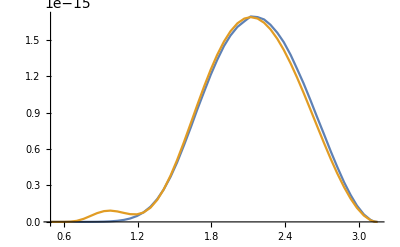

```mathematica
Plot[{Const5π*dΓ5π,Const5πb*dΓ5πb},{q2, 25mπ^2, (m1-m2)^2}]
```

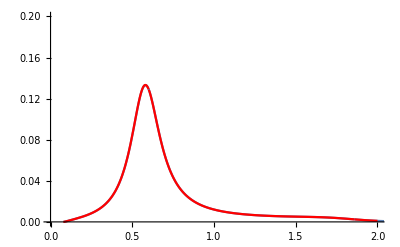

```mathematica
Fq2π1={#[[1]], Const2π#[[2]]}&/@Fq2π;
Show[ListPlot[Fq2π1, Joined->True, PlotRange->{{0, 2}, {0, 0.2}}], Plot[ Const2πb*Fq2πb,{q2, 4mπ^2, 2},PlotStyle->Red, PlotRange->All]]
```

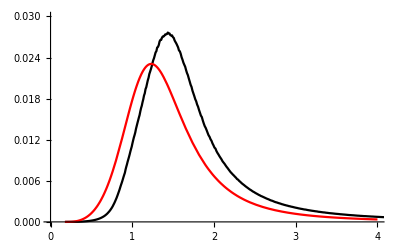

```mathematica
Fq3π1={#[[1]], Const3π#[[2]]}&/@Fq3π;
Show[ListPlot[Fq3π1, Joined->True, PlotRange->{{0, 4}, {0, 0.03}}, PlotStyle->Black], Plot[ Const3πb*Fq3πb,{q2, 9mπ^2, 4},PlotStyle->Red, PlotRange->All]]
```

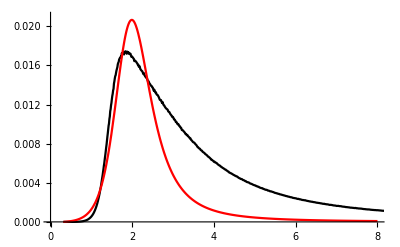

```mathematica
Fq4π1={#[[1]], Const4π#[[2]]}&/@Fq4π;
Show[ListPlot[Fq4π1, Joined->True, PlotRange->{{0, 8}, {0, 0.021}}, PlotStyle->Black], Plot[ Const4πb*Fq4πb,{q2,16mπ^2, 8},PlotStyle->Red, PlotRange->All]]
```

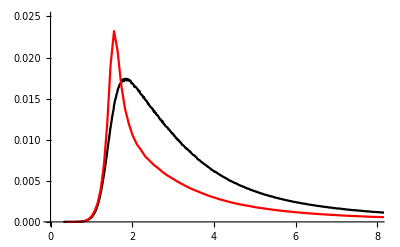

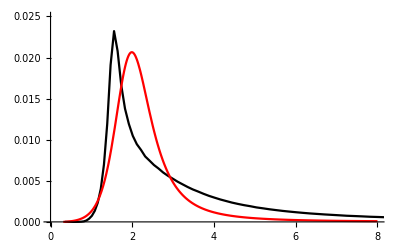

```mathematica
Fq4πinterf1 = {#[[1]], Const4πinterf#[[2]]}&/@Fq4πinterference;
Show[ListPlot[Fq4π1, Joined->True, PlotRange->{{0, 8}, {0, 0.025}}, PlotStyle->Black], ListPlot[Fq4πinterf1, Joined->True, PlotRange->{{0, 8}, {0, 0.025}}, PlotStyle->Red]]
Show[ListPlot[Fq4πinterf1, Joined->True, PlotRange->{{0, 8}, {0, 0.025}}, PlotStyle->Black], Plot[ Const4πb*Fq4πb,{q2,16mπ^2, 8},PlotStyle->Red, PlotRange->All]]
```

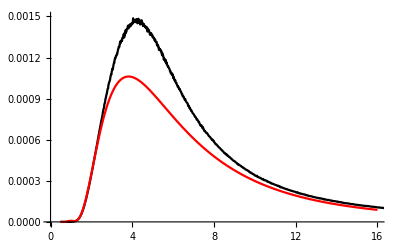

```mathematica
Fq5π1={#[[1]], Const5π#[[2]]}&/@Fq5π;
Show[ListPlot[Fq5π1, Joined->True, PlotRange->{{0, 16}, {0, 0.0015}}, PlotStyle->Black], Plot[ Const5πb*Fq5πb,{q2, 25mπ^2, 16},PlotStyle->Red, PlotRange->All]]
```

## Clear

```mathematica
Clear[Γ2π,Γ3π,Γ4π,Γ5π,dΓ2π,dΓ3π,dΓ4π,dΓ5π,H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ClearScalarProducts;
```

## Init

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,m232,q,m1,m2,m3,m4,Br,f1,f2,g1,g2];
ScalarProduct[p11,p11]=m1^2;
ScalarProduct[p22,p22]=m2^2;
ScalarProduct[p11,p22]=(m1^2+m2^2-m232)/2;
SetMandelstam[m232,m132,m122,p1,-p2,-pe,-ke,m1,m2,0,0];
qq=p11-p22;
q=p1-p2;
sigma=I*(GA[μ].GA[ν]-GA[ν].GA[μ])/2;
H =SpinorUBar[p22,m2].(GA[μ]*f1+I*sigma*FV[qq,ν]*f2/m1).SpinorU[p11, m1]-SpinorUBar[p22,m2].(GA[μ]*g1+ⅈ*sigma*FV[qq,ν]*g2/m1).GA[5].SpinorU[p11, m1];
HH=SpinorUBar[p2,m2].(GA[μ]*f1+I*sigma*FV[q,ν]*f2/m1).SpinorU[p1, m1]-SpinorUBar[p2,m2].(GA[μ]*g1+ⅈ*sigma*FV[q,ν]*g2/m1).GA[5].SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
cHH= ComplexConjugate[HH]/.{μ->α,ν->β};
H2=H*cH;
HH2=HH*cHH;
HH3=DiracSimplify[FermionSpinSum[HH2]]/.{DiracTrace->TR};
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α]-m232*MT[μ,α])]];
λ:=√(1-((m2+√m232)/m1)^2)*√(1-((m2-√m232)/m1)^2);
HT:=λ*H4;
(*T=Transversal*)
HL:=λ*Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α])]];
(*L=Longitudinal*)
L=SpinorUBar[pe].GA[μ].(1+GA[5]).SpinorV[ke];
cL=ComplexConjugate[L]/.{μ->α};
L2=FermionSpinSum[L*cL]/.{DiracTrace->TR};
M2=Simplify[1/2*Gf^2*Calc[HH3*L2]];
M3=M2//.m132->m1^2+m2^2-m122-m232;
E2ZV= (m122-m2^2 +m3^2)/(2*Sqrt[m122]) (*  E2^*  *);
E3ZV= (m1^2-m122-m4^2)/(2*Sqrt[m122])  (*  E3^*  *);
m23min=(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]+Sqrt[E3ZV^2-m4^2])^2;
m23max=Simplify[Calc[(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]-Sqrt[E3ZV^2-m4^2])^2]];
m12min=m2^2;
m12max=m1^2;
```

```mathematica
Clear[Fq2πb,Fq3πb,Fq4πb,Fq5πb,dΓ2πb, dΓ3πb, dΓ4πb, dΓ5πb];
dΓl:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*dm232 /(2*π)*(1/(8*π))*Vckm^2*HT*Fm2320
dΓl1:=(1/2)*(1/(2*π)^3)*(1/(32*m1^3))*Vckm^2*M3;
dΓ2π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const2π*Interpolation[Fq2π][m232];
ret6=ret4/.{q->Sqrt[m232]};
dΓ2πb:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Re[Const2πb]*ret6;
dΓ3π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const3π*Interpolation[Fq3π][m232];
Fq3πb=2.93*10^-5*((m232-9*mπ^2)/m232)^4*(1+190 m232)/((m232-1.06)^2+0.48)^2;
dΓ3πb:=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const3πb*Fq3πb;
dΓ4π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const4π*Interpolation[Fq4π][m232];
Fq4πb=(0.00017983715820604627*(-0.31360000000000005+m232)*(1+5.074780646730226*m232+8.631754238222705*m232^2))/((0.6162735882355033+(-1.834698151162789+m232)^2)^2*m232);
dΓ4πb:=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const4πb*Fq4πb;
dΓ5π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const5π*Interpolation[Fq5π][m232];
Fq5πb=32*((m232-25*mπ^2)/m232)^10*(1-1.65*m232+0.69 m232^2)/((m232+2.21)^2-4.69)^3;
dΓ5πb:=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Const5πb*Fq5πb;
```

## File

```mathematica
SetDirectory[NotebookDirectory[]];
<<"wang_data.m";
decays={#["in"],#["out"]}&/@Normal[DeleteDuplicates[dsFF[All,{"in","out"}]]];
Clear[$FF];
$FF[data_]:=Module[{},Switch[data["func"],"FF",Return[data["F0"]/(1-m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];,"GG",Return[data["F0"]/(1+m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];];];
(*Clear[cS,cA];*)
Clear[FF];
FF[query_]:=Module[{$res},$res=dsFF[query];
Return[cS $FF[$res[1]]+cA $FF[$res[2]]]];
```

## Test

```mathematica
in="\\Omega_{cc}^{+}";
out="\\Omega_{c}^{0}";
testresult={};
AppendTo[testresult,{"in","out","m1-m2","Vckm","l nul","pi" ,"rho/2pi","2pi/2pi_before", "3pi/3pi_before", "4pi/4pi_before", "5pi/5pi_before"}];
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*Vckm^2*Hπ;
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γa1=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\a_1"]&]][[1]]["width"];
(*Γ2π=NIntegrate[dΓ2π, {m232,9mπ^2,(m1-m2)^2}];
Γ2πb=Re[NIntegrate[dΓ2πb, {m232,4mπ^2,(m1-m2)^2}]];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ3πb=NIntegrate[dΓ3πb, {m232,9mπ^2,(m1-m2)^2}];
Γ4π=NIntegrate[dΓ4π, {m232,16mπ^2,(m1-m2)^2}];
Γ4πb=NIntegrate[dΓ4πb, {m232,16mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
Γ5πb=NIntegrate[dΓ5πb, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[testresult,{in,out,Vckm1->Vckm2,Floor[Chop[Γl1/fullΓ],-0.000001]*100,Floor[Chop[Γπ/fullΓ],-0.0000000001]*100,Floor[Chop[Γρ/Γ2π],-0.00000001],Floor[Chop[Γ2π/Γ2πb],-0.0000001],Floor[Chop[Γ3π/Γ3πb],-0.0000001],Floor[Chop[Γ4π/Γ4πb],-0.0000001],Floor[Chop[Γ5π/Γ5πb],-0.0000001]}];*)
AppendTo[testresult,{in,out,m1-m2,Vckm1->Vckm2,1,1,1,1,1,1,1}];
testresult
```

(in | out | m1-m2 | Vckm | l nul | pi | rho/2pi | 2pi/2pi_before | 3pi/3pi_before | 4pi/4pi_before | 5pi/5pi_before
\Omega_{cc}^{+} | \Omega_{c}^{0} | 0.955 | c→s | 1 | 1 | 1 | 1 | 1 | 1 | 1)

```mathematica
Plot[{Fq3π, Fq3πb}, {m232, 9mπ^2, (m1-m2)^2}]
```

$Aborted

## Main calculation

```mathematica
result={};
AppendTo[result,{"in","out","Vckm","l nul","pi" ,"rho/2pi","2pi/2pi_before", "3pi/3pi_before", "4pi/4pi_before", "5pi/5pi_before"}];
i=.0;
PrintTemporary[Dynamic[dec],"Завершено",Dynamic[Floor[i/36*100,-0.1]], "%" ];
Do[
{in,out}=dec;
i=i+1;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*Vckm^2*Hπ;
Ha1=HT/.{m232-> ma1^2};
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,4mπ^2,(m1-m2)^2}];
Γ2πb=Re[NIntegrate[dΓ2πb, {m232,4mπ^2,(m1-m2)^2}]];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ3πb=NIntegrate[dΓ3πb, {m232,9mπ^2,(m1-m2)^2}];
Γ4π=NIntegrate[dΓ4π, {m232,16mπ^2,(m1-m2)^2}];
Γ4πb=NIntegrate[dΓ4πb, {m232,16mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
Γ5πb=NIntegrate[dΓ5πb, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[result,{in,out,Vckm1->Vckm2,Floor[Chop[Γl1/fullΓ],-0.000001]*100,Floor[Chop[Γπ/fullΓ],-0.0000000001]*100,Floor[Chop[Γρ/Γ2π],-0.00000001],Floor[Chop[Γ2π/Γ2πb],-0.0000001],Floor[Chop[Γ3π/Γ3πb],-0.0000001],Floor[Chop[Γ4π/Γ4πb],-0.0000001],Floor[Chop[Γ5π/Γ5πb],-0.0000001]}];
,{dec,decays}];
result
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m232} = TraditionalForm`{0.04309}. NIntegrate obtained TraditionalForm`6.199949246656747`*^-14 and TraditionalForm`2.7953540267495105`*^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`18 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m122, m232} = TraditionalForm`{0.468141, 0.0332227}. NIntegrate obtained TraditionalForm`6.200280512010538`*^-14 and TraditionalForm`5.231484967839733`*^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m232} = TraditionalForm`{0.0429364}. NIntegrate obtained TraditionalForm`6.139831083689381`*^-14 and TraditionalForm`2.321958443411979`*^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

(in | out | Vckm | l nul | pi | rho/2pi | 2pi/2pi_before | 3pi/3pi_before | 4pi/4pi_before | 5pi/5pi_before
\Xi_{cc}^{++} | \Lambda_{c}^{+} | c→d | 0.4936 | 0.377359 | 1.15032 | 1.00003 | 0.851294 | 1.0561 | 0.817935
\Xi_{cc}^{++} | \Sigma_{c}^{+} | c→d | 0.4503 | 0.301942 | 1.16625 | 1.0002 | 0.688142 | 0.75354 | 0.380076
\Xi_{cc}^{++} | \Xi_{c}^{+} | c→s | 4.9858 | 8.30163 | 1.2266 | 0.999725 | 0.535003 | 0.472047 | 0.148659
\Xi_{cc}^{++} | \Xi_{c}^{\prime+} | c→s | 5.975 | 6.92904 | 1.24937 | 0.999994 | 0.460616 | 0.284811 | 0.0427094
\Xi_{cc}^{+} | \Sigma_{c}^{0} | c→d | 0.2988 | 0.201094 | 1.16683 | 1.00019 | 0.686211 | 0.74914 | 0.375171
\Xi_{cc}^{+} | \Xi_{c}^{0} | c→s | 1.6513 | 2.74944 | 1.2266 | 0.999725 | 0.535003 | 0.472047 | 0.148659
\Xi_{cc}^{+} | \Xi_{c}^{\prime0} | c→s | 1.984 | 2.30995 | 1.25011 | 0.999992 | 0.458914 | 0.282288 | 0.0419155
\Omega_{cc}^{+} | \Xi_{c}^{0} | c→d | 0.2079 | 0.293426 | 1.21767 | 0.999813 | 0.579815 | 0.569687 | 0.21936
\Omega_{cc}^{+} | \Xi_{c}^{\prime0} | c→d | 0.2492 | 0.244044 | 1.23155 | 1.00007 | 0.501258 | 0.348682 | 0.0655402
\Omega_{cc}^{+} | \Omega_{c}^{0} | c→s | 6.6604 | 11.1885 | 1.33644 | 0.999715 | 0.300507 | 0.118358 | 0.0084711
\Xi_{bb}^{0} | \Sigma_{b}^{+} | b→u | 0.0043 | 1.43×10^-6 | 1.02313 | 1.0002 | 1.27972 | 2.05822 | 10.1385
\Xi_{bb}^{0} | \Xi_{bc}^{+} | b→c | 2.5911 | 0.00347432 | 1.05065 | 1.00014 | 1.22307 | 1.78691 | 1.28958
\Xi_{bb}^{0} | \Xi_{bc}^{\prime+} | b→c | 1.1503 | 0.00062621 | 1.02227 | 1.0002 | 1.28226 | 2.0925 | 1.28866
\Xi_{bb}^{-} | \Lambda_{b}^{0} | b→u | 0.0011 | 8.3×10^-7 | 1.04512 | 1.00015 | 1.22794 | 1.739 | 9.06283
\Xi_{bb}^{-} | \Sigma_{b}^{0} | b→u | 0.0022 | 7.2×10^-7 | 1.02314 | 1.0002 | 1.27972 | 2.0583 | 10.3115
\Xi_{bb}^{-} | \Xi_{bc}^{0} | b→c | 2.6207 | 0.00348729 | 1.05062 | 1.00014 | 1.2232 | 1.78821 | 1.28941
\Xi_{bb}^{-} | \Xi_{bc}^{\prime0} | b→c | 1.1556 | 0.0006233 | 1.02224 | 1.0002 | 1.28243 | 2.09472 | 1.28837
\Omega_{bb}^{-} | \Xi_{b}^{0} | b→u | 0.002 | 1.64×10^-6 | 1.04525 | 1.00015 | 1.22694 | 1.72759 | 6.9762
\Omega_{bb}^{-} | \Xi_{b}^{\prime0} | b→u | 0.0044 | 1.44×10^-6 | 1.02321 | 1.0002 | 1.27866 | 2.04325 | 10.3638
\Omega_{bb}^{-} | \Omega_{bc}^{0} | b→c | 4.8074 | 0.00702028 | 1.0512 | 1.00014 | 1.22085 | 1.76261 | 1.29261
\Omega_{bb}^{-} | \Omega_{bc}^{\prime0} | b→c | 2.1266 | 0.00125917 | 1.02197 | 1.0002 | 1.28083 | 2.06122 | 1.29388
\Xi_{bc}^{+} | \Lambda_{b}^{0} | c→d | 0.2234 | 0.0438203 | 1.17132 | 0.999997 | 0.779748 | 0.989611 | 0.701585
\Xi_{bc}^{+} | \Sigma_{b}^{0} | c→d | 0.1483 | 0.0305532 | 1.2145 | 1.0001 | 0.548493 | 0.439649 | 0.110899
\Xi_{bc}^{+} | \Xi_{b}^{0} | c→s | 2.3 | 0.927201 | 1.23726 | 0.999697 | 0.500806 | 0.398167 | 0.103997
\Xi_{bc}^{0} | \Sigma_{b}^{-} | c→d | 0.1121 | 0.0232861 | 1.21583 | 1.0001 | 0.544937 | 0.432444 | 0.106793
\Xi_{bc}^{0} | \Xi_{b}^{-} | c→s | 0.8684 | 0.352921 | 1.23795 | 0.999693 | 0.497685 | 0.391766 | 0.100563
\Omega_{bc}^{0} | \Xi_{b}^{-} | c→d | 0.2542 | 0.0383789 | 1.15361 | 1.00004 | 0.842921 | 1.04927 | 0.809293
\Omega_{bc}^{0} | \Omega_{b}^{-} | c→s | 6.0272 | 1.25182 | 1.222 | 1.00007 | 0.529502 | 0.403094 | 0.0913874
\Xi_{bc}^{+} | \Sigma_{c}^{++} | b→u | 0.0035 | 2.63×10^-6 | 1.0274 | 1.00018 | 1.28399 | 2.23507 | 19.6067
\Xi_{bc}^{+} | \Xi_{cc}^{++} | b→c | 1.5843 | 0.00802878 | 1.05753 | 1.00012 | 1.20682 | 1.69943 | 1.29097
\Xi_{bc}^{0} | \Lambda_{c}^{+} | b→u | 0.0003 | 5.1×10^-7 | 1.04836 | 1.00014 | 1.22872 | 1.83069 | 21.0455
\Xi_{bc}^{0} | \Sigma_{c}^{+} | b→u | 0.0007 | 5.×10^-7 | 1.0274 | 1.00018 | 1.284 | 2.2352 | 19.8072
\Xi_{bc}^{0} | \Xi_{cc}^{+} | b→c | 0.6027 | 0.00305399 | 1.05753 | 1.00012 | 1.20682 | 1.69943 | 1.29097
\Omega_{bc}^{0} | \Xi_{c}^{+} | b→u | 0.0005 | 9.4×10^-7 | 1.04771 | 1.00014 | 1.22878 | 1.81425 | 17.2272
\Omega_{bc}^{0} | \Omega_{cc}^{+} | b→c | 1.8684 | 0.00663499 | 1.05534 | 1.00013 | 1.21369 | 1.75871 | 1.28484)